# Tanabe - Sugano Diagrams ~With Spin - Orbit~ ---------------------------------------------------

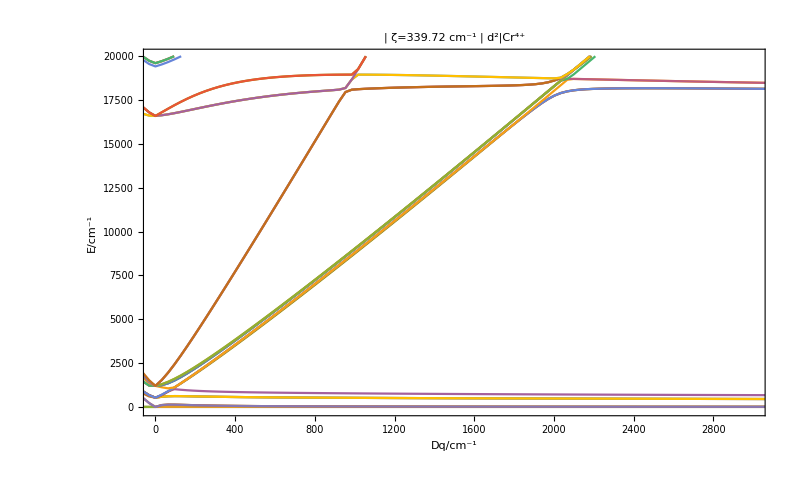
This notebook can be used to explore the approximate multiplet structure of transition metal ions under the influence of the crystal field of a solid host. 
This approximation is obtained by applying perturbation theory to the degenerate ground state defined by the free-ion Hamiltonian (which excludes the e-e repulsion). The perturbation terms include the crystal field (parametrized by a single parameter for the symmetries included here), the spin-orbit relativistic term, and the e-e Coulomb repulsion.
Graphs show the energy levels (with respect to the ground level which is always shown as a horizontal line in the bottom) as a function of the strength of the crystal field.

-Graphics-

Finding the matrix elements corresponding to the e-e repulsion requires the values for the Racah parameters (B, C). The values for these are taken from the Hartree-Fock approximation implemented by Cowan and recomputed by Brik and Ma.
Here only the cubic case is shown, but negative values for Dq can also be explored, so as to approximate what occurs in tetrahedral or octahedral symmetries.

References:
* Brik, M. G., & Ma, C. G. (2019). Theoretical Spectroscopy of Transition Metal and Rare Earth Ions: From Free State to Crystal Field.
* Cowan, R. D. (1981). The theory of atomic structure and spectra.

## Data Loader

```mathematica
SetDirectory[NotebookDirectory[]];
h5File="tsk_diag_withSO_HF-final-highres.h5";
shellToatoms=<|
"3d"->StringSplit["Sc Ti V Cr Mn Fe Co Ni Cu Zn"," "],
"4d"->StringSplit["Y Zr Nb Mo Tc Ru Rh Pd Ag Cd"," "],
"5d"->StringSplit["Lu Hf Ta W Re Os Ir Pt Au Hg"," "]|>;
evtocm=8065.544290;
datakeys = Import[h5File];
HFdata=Association[Table[key->Import[h5File,key],{key,datakeys}]];
energiesTemplate=StringTemplate["/`atom`/`charge`/energies"];
DqsTemplate=StringTemplate["/`atom`/`charge`/Dqs"];
cowandata=Import["brik_and_ma_from_cowan.xlsx"][[1]];
headers=cowandata[[1]];
cowandata=cowandata[[2;;]];
cowanA=Association[{#[[1]],Round[#[[2]]]}->Association[{"d^n"->Round[#[[4]]],
"B"->Round[#[[6]]],
"C"->#[[7]],
"ζ"->#[[11]],
"C/B"->Round[#[[7]]/#[[6]],0.1]
}]&/@cowandata];
```

## Diagrams

The line colors here are not meaningful, and are shown merely as a guide to the eye.

```mathematica
Manipulate[(
ekey=energiesTemplate[<|"atom"->atom,"charge"->charge|>];
dqkey=DqsTemplate[<|"atom"->atom,"charge"->charge|>];
If[Not[MemberQ[Keys[HFdata],dqkey]],
"Not a valid ion, try a different charge.",(
energies=Transpose[HFdata[ekey]];
Dqs=HFdata[dqkey];
numElectrons=cowanA[{atom,charge}]["d^n"];
extraTicks=Table[{ee*evtocm,ee},{ee,0,Erange[[2]]/evtocm,0.25}];
moTicks=Table[{ee*evtocm,ee},{ee,Floor[Dqrange[[1]]/evtocm],Ceiling[Dqrange[[2]]/evtocm],0.1}];
so=Round[cowanA[{atom,charge}]["ζ"]];
plotTitle=Row[{"| ζ=",so," cm^-1 | ",Superscript["d",numElectrons],"|",Superscript[atom,ToString[charge]<>"+"]},BaseStyle->"Title"];
ListPlot[Table[Transpose[{Dqs,row}],{row,energies}],
Frame->True,
Joined->joined,
ImageSize->1200,
FrameLabel->{{"E/cm^-1","E/eV"},{"Dq/cm^-1","Dq/eV"}},
PlotLabel->Framed[plotTitle],
FrameStyle->Directive[20],
FrameTicks->{{Automatic,extraTicks},{Automatic,moTicks}},
PlotRange->{Dqrange,Erange}])
]
),
Row[{Column[{Control[{{shell,"3d"},{"3d","4d","5d"}}],
Control[{{atom,"Cr"},shellToatoms[shell],ControlType->SetterBar}],
Control[{{charge,3},{2,3,4,5,6,7},ControlType->RadioButton}]
}],
Column[{Control[{{Dqrange,{0,3000}},-10000,10000,ControlType->IntervalSlider}],
Control[{{Erange,{-100,20000}},-1000,60000,ControlType->IntervalSlider}],
Control[{{joined,True},{True,False}}]
}]
}],
TrackedSymbols:>{shell,atom,charge,Dqrange,Erange,joined}]
```